### Champions

#### Kalista

20+(3 AD)/5+10 rank

10+AD (1/5+rank/40)+(7 rank)/2+rank^2/2

<|DMG→20+(3 AD)/5+10 rank+hits (10+AD (1/5+rank/40)+(7 rank)/2+rank^2/2),MP→40,CD→14-(3 rank)/2|>

{{0,14},{1,12.5},{2,11},{3,9.5},{4,8}}

14.-1.5 rank

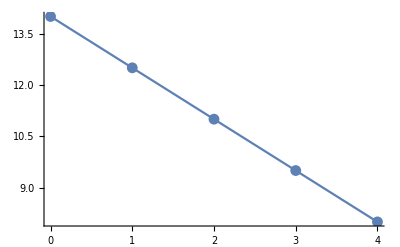

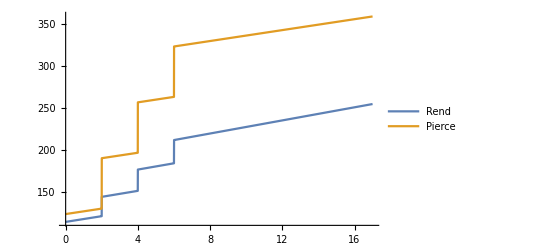

```mathematica
kalista = <| HP -> 51776/100 + lv 83,
			 MP -> 2318/10 + lv 35,
			 MPRegen -> 63/10 + lv 4/10,
			 AD -> 5346/100 + lv 325/100,
			 AS -> 0658/1000 + lv 0033/1000,
			 AR -> 19012/1000 + lv 35/10,
			 MR -> 30 |>;

pierce = <| DMG -> 10 + 60rank + AD, MP -> 50 + 5 rank, CD -> 8 |>;

rendbasedmg = (20 + 10rank) + (AD * 6/10)
rendperhitdmg = (10 + 35/10 rank + 1/2 rank^2) + (AD * (20/100 + 25/1000 rank))
rend = <| DMG -> rendbasedmg + (hits * rendperhitdmg), MP -> 40, CD -> 14 - 15/10 rank |>

ddat = {{0,14},{1,12.5},{2,11},{3,9.5},{4,8}}
func = Fit[ddat, {1,rank}, rank]
Show[ListPlot[ddat], Plot[func, {rank,0,4}]]

Plot[{rend[DMG]   //. {rank -> Min[4, 1 + Quotient[lv,2]], hits -> 2, AD -> kalista[AD]},
	  pierce[DMG] //. {rank -> Min[4, 1 + Quotient[lv,2]], hits -> 2, AD -> kalista[AD]}}, {lv,0,17}, PlotLegends->{"Rend","Pierce"}]
```

#### Katarina

{{0,60},{1,85},{2,110},{3,135},{4,160}}

60.+25. rank

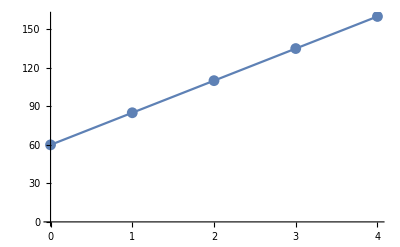

{rank→Min[4,1+Quotient[lv,2]],rankU→Min[2,Quotient[lv,6]],AD→7297/125+(16 lv)/5,BonusAD→0,AP→0}

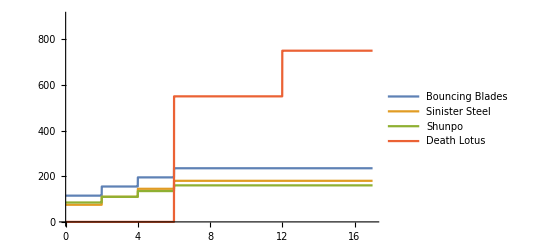

```mathematica
katarina = <| HP -> 5594/10 + lv 80,
			 MP -> Infinity,
			 MPRegen -> 63/10 + lv 4/10,
			 AD -> 58376/1000 + lv 32/10,
			 AS -> 0658/1000 + lv 00274/10000,
			 AR -> 2688/100 + lv 35/10,
			 MR -> 321/10 + lv 125/100 |>;

bouncingbladeNoProc = <| DMG -> 60 + 25rank + (AP 45/100), MP -> 0 rank, CD -> 10 - rank 1/2 |>;
bouncingblade = <| DMG -> 75 + 40rank + (AP 60/100), MP -> 0 rank, CD -> 10 - rank 1/2 |>;
sinistersteel = <| DMG -> 40 + 35rank + (AP 25/100) + (BonusAD 60/100), MP -> 0 rank, CD -> 4 |>;
shunpo = <| DMG -> 60 + 25rank + (AP 40/100), MP -> 0, CD -> 12 - rank 3/2 |>;

deathlotus = <| DMG -> 350 + 200rankU + (AP 250/100) + (BonusAD 375/100), MP -> 0, CD -> 90 - 375/10 rankU - 75/10 rankU^2 |>;
 

ddat = {{0,60},{1,85},{2,110},{3,135},{4,160}}
func = Fit[ddat, {1,rank}, rank]
Show[ListPlot[ddat], Plot[func, {rank,0,4}]]

env = {rank -> Min[4, 1 + Quotient[lv,2]], rankU -> Min[2, Quotient[lv,6]], AD -> katarina[AD], BonusAD -> 0, AP -> 0} 
Plot[{bouncingblade[DMG] //. env, 
	  sinistersteel[DMG] //. env,
	  shunpo[DMG] //. env,
	  Piecewise[{{deathlotus[DMG] //. env, lv ≥ 6}}, 0]
	}, {lv,0,17}, PlotLegends->{"Bouncing Blades","Sinister Steel","Shunpo","Death Lotus"}, PlotRange -> {0,900}] 

Unset[{env,ddat,func}];
```

```mathematica
katTradePattern0 = bouncingbladeNoProc[DMG] * mresist * tradeBonusMR  //. {EffectiveAR -> EnemyAR, EffectiveMR -> EnemyMR}
katTradePattern1 = (bouncingblade[DMG] + sinistersteel[DMG] + shunpo[DMG] * mresist * tradeBonusMR) + (AD * armor * tradeBonusAR) //. {EffectiveAR -> EnemyAR, EffectiveMR -> EnemyMR}
opt = Join[runexform[katarina], {EnemyAR -> enemy[AR] - ARPen, EnemyMR -> enemy[MR] - MRPen, rank -> Quotient[lv,2], lv -> 3}];
variables = Flatten[{qvars,yellowvars,bluevars,redvars}];

NMaximize[{katTradePattern1,cs} //. opt, variables, Integers, MaxIterations -> 2000] /. {(a_ -> 0) :> Sequence[]}
NMaximize[{katTradePattern0,cs} //. opt, variables, Integers, MaxIterations -> 2000] /. {(a_ -> 0) :> Sequence[]}

Unset[opt]
Unset[variables]
```

(100 (2-100/(100+MR)) (60+(9 AP)/20+25 rank))/(100+EnemyMR)

115+(17 AP)/20+(3 BonusAD)/5+(100 AD (2-100/(100+AR)))/(100+EnemyAR)+75 rank+(100 (2-100/(100+MR)) (60+(2 AP)/5+25 rank))/(100+EnemyMR)

{371.418,{qnAP→3,ynAP→9,bnAP→9,rnAD→9}}

{86.8783,{qnAP→3,ynMR→9,bnMR→9,rnMRPen→9}}

```mathematica
window = 10

actions[champ_,ability_] := <| APSMP -> (MPRegen/5 / ability[MP]), APT -> MP / ability[MP], APSCD -> 1/ability[CD] |>


window * N[actions[kalista,pierce][APSMP] /. {lv -> 6, rank -> 3}]
window * N[actions[kalista,rend][APSMP] /. {lv -> 6, hits -> 1, rank -> 3}]
window * kalista[AS] /. lv -> 6.0
aapoke = (AD * hits) 
armor = 100/(100+EffectiveAR)

mresist =100/(100+EffectiveMR)

enemyMitigation = armor /. {EffectiveAR -> (EnemyAR - ARPen)}
tradeBonusAR = 2 - armor /. {EffectiveAR -> AR}
tradeBonusMR = 2 - mresist /. {EffectiveMR -> MR}

2 - mitigation /. {EnemyAR -> 30, ARPen -> 0.0}
2 - mitigation /. {EnemyAR -> 40, ARPen -> 0.0}
runexform[champ_] := { ARPen   -> amount[ARPen], 
					   MRPen   -> amount[MRPen],
  					 AD      -> champ[AD] + amount[AD],
					   BonusAD -> amount[AD], 
					   AP      -> amount[AP],
  					 AS      -> champ[AS] + amount[AS],
					   AR      -> champ[AR] + amount[AR],
					   MR      -> amount[MR],
					   MP      -> champ[MP],
  					 MPRegen -> champ[MPRegen] + amount[MPRegen] + 3
 					}
std[champ_] := { ARPen -> 0, AD -> champ[AD] + 15, AS -> champ[AS], AR -> champ[AR] + 10, MP -> champ[MP], MPRegen -> champ[MPRegen] }
aspd = Floor[25/10*AS]

(*
poke[champ_,ability_] := (window * actions[champ,ability][APSMP] + actions[champ,ability][APT])  (ability[DMG] + aapoke) enemyMitigation defenseBonus
shoot = aapoke enemyMitigation defenseBonus 
*)
enemy = kalista;


(*Min[actions[champ,ability][APSCD], actions[champ,ability][APSMP]]*)
poke[champ_,ability_] := trades  (ability[DMG] + aapoke) armor
shoot[enemy_] := aapoke mitigation[enemy]

pokeOut[champ_,ability_] := poke[champ,ability] //. EffectiveArmor -> EnemyAR
pokeIn[champ_,ability_] := poke[champ,ability] //. std[champ] //. EffectiveArmor -> AR (* Flatten[{std[enemy], EffectiveArmor -> AR}] *)
pokeOut[kalista,pierce]
```

10

0.0307692 MPRegen

0.05 MPRegen

8.56

AD hits

100/(100+EffectiveAR)

100/(100+EffectiveMR)

100/(100-ARPen+EnemyAR)

2-100/(100+AR)

2-100/(100+MR)

2-mitigation

2-mitigation

Floor[(5 AS)/2]

(100 (10+AD+AD hits+60 rank) trades)/(100+EffectiveAR)

```mathematica
opt = Join[runexform[kalista], {EnemyAR -> enemy[AR] - ARPen, hits -> 1, rank -> Quotient[lv,2], lv -> 6}];
variables = Flatten[{trades,qvars,yellowvars,bluevars,redvars}];
actions[kalista,pierce][APT] //. {rank -> 2.0, lv -> 2, MP -> kalista[MP] }
cs = Flatten[{
	Total@redvars == 9,
	Total@yellowvars == 9,
	Total@qvars == 3,
	Total@bluevars == 9,
	Map[{# ≥ 0, # ≤ 9}&, redvars],
	Map[{# ≥ 0, # ≤ 3}&, qvars],
	Map[{# ≥ 0, # ≤ 9}&, yellowvars],
	Map[{# ≥ 0, # ≤ 9}&, bluevars]
	}];

(opt //. { (a_ -> b_) :> {a,b} }) // MatrixForm
Off[NMaximize::incst]

attack = rend
{
	pokeOut[kalista,attack] - pokeIn[kalista,attack],
    {
		cs,
        pokeIn[kalista,attack] ≤ kalista[HP],
        pokeOut[enemy,attack] ≥ enemy[HP],
        trades > 0
	}
} //. opt
NMaximize[%, variables, Integers, MaxIterations -> 2000] /. {(a_ -> 0) :> Sequence[]}
(*
N@poke[kalista,pierce,enemy] //. opt //. runes
kalista[HP] /. lv -> 6.0 *)

(*
NMaximize[{poke[kalista,rend], cs} //. opt, variables, Integers, MaxIterations -> 800] /. {(a_ -> 0) :> Sequence[]}
NMaximize[{poke[kalista,pierce], cs} //. opt, variables, Integers, MaxIterations -> 800] /. {(a_ -> 0) :> Sequence[]} *)
(*NMaximize[{shoot, cs} //. opt, variables, Integers, MaxIterations-> 2000] /. {(a_ -> 0) :> Sequence[]}*)
```

5.03

(ARPen | (13 qnARPen)/5+(32 rnARPen)/25
AD | 2673/50+(7 bnAD)/25+(13 lv)/4+(23 qnAD)/10+(19 rnAD)/20+(43 ynAD)/100
AS | 329/500+(4 bnAS)/625+(33 lv)/1000+(9 qnAS)/200+(17 rnAS)/1000+(19 ynAS)/2500
AR | 4753/250+(7 bnAR)/10+(7 lv)/2+(43 qnAR)/10+(91 rnAR)/100+ynAR
MP | 1159/5+35 lv
MPRegen | 93/10+(33 bnMPRegen)/100+(2 lv)/5+(13 qnMPRegen)/10+(13 rnMPRegen)/50+(41 ynMPRegen)/100
EnemyAR | 4753/250+(7 lv)/2
hits | 1
rank | Quotient[lv,2]
lv | 6)

<|DMG→20+(3 AD)/5+10 rank+hits (10+AD (1/5+rank/40)+(7 rank)/2+rank^2/2),MP→40,CD→14-(3 rank)/2|>

{(25000 trades (3699/25+(7 bnAD)/25+(23 qnAD)/10+(19 rnAD)/20+7/8 (1824/25+(7 bnAD)/25+(23 qnAD)/10+(19 rnAD)/20+(43 ynAD)/100)+(43 ynAD)/100))/35003-(47985 trades)/(2 (35003/250+(7 bnAR)/10+(43 qnAR)/10+(91 rnAR)/100+ynAR)),{{rnAD+rnAP+rnAR+rnARPen+rnAS+rnMPRegen+rnMR+rnMRPen==9,ynAD+ynAP+ynAR+ynARPen+ynAS+ynMPRegen+ynMR+ynMRPen==9,qnAD+qnAP+qnAR+qnARPen+qnAS+qnMPRegen+qnMR+qnMRPen==3,bnAD+bnAP+bnAR+bnARPen+bnAS+bnMPRegen+bnMR+bnMRPen==9,rnAS≥0,rnAS≤9,rnAD≥0,rnAD≤9,rnARPen≥0,rnARPen≤9,rnMPRegen≥0,rnMPRegen≤9,rnAR≥0,rnAR≤9,rnMR≥0,rnMR≤9,rnMRPen≥0,rnMRPen≤9,rnAP≥0,rnAP≤9,qnAS≥0,qnAS≤3,qnAD≥0,qnAD≤3,qnARPen≥0,qnARPen≤3,qnMPRegen≥0,qnMPRegen≤3,qnAR≥0,qnAR≤3,qnMR≥0,qnMR≤3,qnMRPen≥0,qnMRPen≤3,qnAP≥0,qnAP≤3,ynAS≥0,ynAS≤9,ynAD≥0,ynAD≤9,ynARPen≥0,ynARPen≤9,ynMPRegen≥0,ynMPRegen≤9,ynAR≥0,ynAR≤9,ynMR≥0,ynMR≤9,ynMRPen≥0,ynMRPen≤9,ynAP≥0,ynAP≤9,bnAS≥0,bnAS≤9,bnAD≥0,bnAD≤9,bnARPen≥0,bnARPen≤9,bnMPRegen≥0,bnMPRegen≤9,bnAR≥0,bnAR≤9,bnMR≥0,bnMR≤9,bnMRPen≥0,bnMRPen≤9,bnAP≥0,bnAP≤9},(47985 trades)/(2 (35003/250+(7 bnAR)/10+(43 qnAR)/10+(91 rnAR)/100+ynAR))≤25394/25,(25000 trades (3699/25+(7 bnAD)/25+(23 qnAD)/10+(19 rnAD)/20+7/8 (1824/25+(7 bnAD)/25+(23 qnAD)/10+(19 rnAD)/20+(43 ynAD)/100)+(43 ynAD)/100))/35003≥25394/25,trades>0}}

{104.901,{trades→6,qnAD→3,ynAR→9,bnAR→9,rnAD→9}}

```mathematica
`
```

### Runes

```mathematica
stats = {AS,AD,ARPen,MPRegen,AR,MR,MRPen,AP};

marks = <| vAS -> 17/1000,
 	      vAD -> 95/100,
 	      vAR -> 91/100,
		   vARPen -> 128/100,
		   vMPRegen -> 26/100,
		   vMRPen   -> 87/100,
           vAP -> 59/100,
		   vMR -> 77/100
		 |>;

seals = <| vAS -> 76/10000,
 	      vAD -> 43/100,
 	      vAR -> 1,
		   vARPen -> 0,
		   vMPRegen -> 41/100,
		   vMRPen -> 0,
		   vAP -> 59/100,
		   vMR -> 74/100
		 |>;

glyphs = <| vAS -> 64/10000,
 	      vAD -> 28/100,
 	      vAR -> 7/10,
		   vARPen -> 0,
		   vMPRegen -> 33/100,
		   vMRPen -> 63/100,
		   vAP -> 119/100,
		   vMR -> 134/100
		 |>;

quints = <| vAS -> 45/1000,
 	      vAD -> 23/10,
 	      vAR -> 43/10,
		   vARPen -> 26/10,
		   vMPRegen -> 13/10,
		   vMRPen -> 201/100,
		   vAP -> 495/100,
		   vMR -> 4
		 |>;

sym[a_,b_] := Symbol[ToString[a] <> ToString[b]]
amount[t_] := (marks[sym[v,t]]*sym[rn,t]) + (quints[sym[v,t]]*sym[qn,t]) + (seals[sym[v,t]]*sym[yn,t]) + (glyphs[sym[v,t]]*sym[bn,t])

redvars = Map[sym[rn,#]&,stats];
yellowvars = Map[sym[yn,#]&,stats];
bluevars = Map[sym[bn,#]&,stats];
qvars = Map[sym[qn,#]&,stats];
```

```mathematica
vars[r_] := Table[Symbol[r <> ToString[i]],{i,0,8}];
set[c_] := Map[vars[c <> #]&,stats]

N[17/1000]

(*Total@Map[amount, stats]*)
(*(kalista[AS] + amount[AS]) * (kalista[AD] + amount[AD]) + (kalista[AR] + amount[AR])*)

(*window[s_] := Floor[s*25/10]
window[4/10]
Plot3D[window[kalista[AS] + amount[AS]], {lv,0,18}, {rnAS,0,9}];


cs = Flatten[{
	Total@redvars == 9,
	Total@qvars == 3,
	Map[# ≥ 0 && # ≤ 9&, redvars],
	Map[# ≥ 0 && # ≤ 3&, qvars],
	EnemyAR ≥ 0,
	rnMPRegen == 0,
	qnMPRegen == 0,
	hits == aspd}];
TableForm[%]
aspd /. {rnAS -> 9, lv -> 1}

NMaximize[FullSimplify[{metric, cs} //. {lv -> 1,EnemyAR -> 30}], Flatten[{hits,qvars,redvars}], Reals]
NMaximize[FullSimplify[{metric, cs} //. {lv -> 1,EnemyAR -> 30}], Flatten[{hits,qvars,redvars}], Integers] *)
```

0.017

0.0641026

-4.67692

262.96

202.277

168.564

(100 AD (2-100/(100+AR)) hits)/(100-ARPen+EnemyAR)

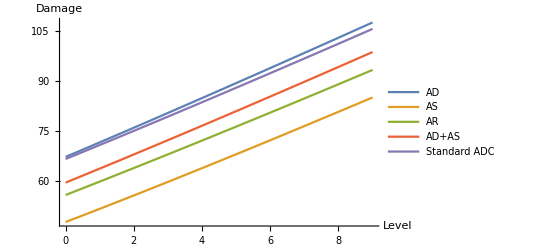

```mathematica
opt2 = Join[runexform[kalista], {rank -> Quotient[lv,2], EnemyAR -> 30}];
zerovars = Thread[variables -> 0];
(2 - armor /. EffectiveArmor -> 30.0) - (2 - armor /. EffectiveArmor -> 20.0)
kalista[AD] - kalista[AD] * (1 + %) /. lv -> 6
pierce[DMG] //. {rank -> 3, AD -> kalista[AD], lv -> 6.0}
% * armor /. EffectiveArmor -> 30.0 
% * armor /. EffectiveArmor -> 20.0 
shoot 
Plot[{
(*	% //. Flatten[{ opt2, rnARPen -> 9, ynARPen -> 9, bnARPen -> 9, qnARPen -> 3, hits -> aspd, zerovars  }], *)
	% //. Flatten[{ opt2, rnAD -> 9, ynAD -> 9, bnAD -> 9, qnAD -> 3, hits -> 1, zerovars }],
	% //. Flatten[{ opt2, rnAS -> 9, ynAS -> 9, bnAS -> 9, qnAS -> 3, hits -> 1, zerovars }],
	% //. Flatten[{ opt2, rnAR -> 9, ynAR -> 9, bnAR -> 9, qnAR -> 3, hits -> 1, zerovars }],
	% //. Flatten[{ opt2, rnAD -> 5, rnAS -> 4, qnAD -> 2, qnAS -> 1, ynAD -> 9, bnAS -> 9, hits -> 1, zerovars }],
	% //. Flatten[{ opt2, rnAD -> 9, qnAD -> 3, ynAR -> 9, bnAR -> 9, hits -> 1, zerovars }]
	},
	{lv,0,9}, PlotLegends -> {"AD","AS","AR","AD+AS","Standard ADC"}, AxesLabel -> {"Level","Damage"} ]
```

### MPRegen : Cooldown bottlenecks

After a certain amount of MP regen we become limited by the actual cooldown of the ability.

#### Ability: Pierce

```mathematica
actions[kalista,pierce][APSMP] ≥ actions[kalista,pierce][APSCD] //. rank -> Quotient[lv,2]
```

MPRegen/(5 (50+5 Quotient[lv,2]))≥1/8

replace the Quotient[] integer division so Reduce works properly

```mathematica
% //. { Quotient[lv,2] -> (lv/2)}
```

MPRegen/(5 (50+(5 lv)/2))≥1/8

lv≥0&&MPRegen≥1/16 (500+25 lv)

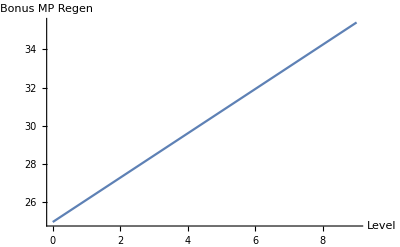

```mathematica
Reduce[{%, lv ≥ 0}, {lv,MPRegen}]
Plot[1/80 (1996+93 lv), {lv,0,9}, AxesLabel-> {"Level","Bonus MP Regen"}]
```

#### Ability: Rend

```mathematica
actions[kalista,rend][APSMP] ≥ actions[kalista,rend][APSCD] //. rank -> Quotient[lv,2]
```

MPRegen/200≥1/(14-3/2 Quotient[lv,2])

```mathematica
% //. { Quotient[lv,2] -> (lv/2)}
```

MPRegen/200≥1/(14-(3 lv)/4)

0≤lv≤18&&MPRegen≥-800/(-56+3 lv)

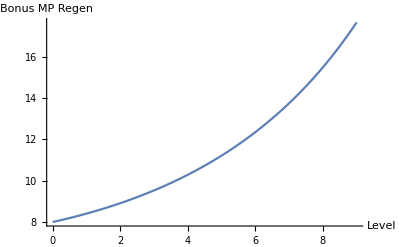

```mathematica
Reduce[{lv ≥ 0, lv ≤ 18, %}, {lv,MPRegen}]
Plot[(-4472+35 lv-12 lv^2)/(-560+30 lv), {lv,0,9}, AxesLabel-> {"Level","Bonus MP Regen"}]
```